# Economics 382 Exam Reviews

7

Uncertainty and Information

## Statistics

Random Variable: A random variable is a variable that records, in numerical form, the possible outcomes for some random event.

Probability Density Function (PDF): A function that shows the probabilities associated with the possible outcomes of a random variable

Expected Value of a Random Variable: The outcome of a random variable that will occur “on average”. The expected value is denoted by E(x). If x is a discrete random variable with n outcomes then E (x)  = (∑^n)_(i=1)x_i = f(x_i), where f(x) is the PDF for the random variable x. If x is a continuous random variable then E(x) = ∫_(-∞)^∞ f(x)*x dx.

Variance and Standard Deviation of a random Variable:  The concepts measure the dispersion of a random variable about its expected value. In the discrete case, Var(x) = σ_x^2 = (∑^n)_(i=1)[x_i-E(x)]^2 f(x_1); in the  continuous case, Var(x) = σ_x^2 = ∫_(-∞)^∞ [x-E(x)]^2 f(x)dx. The standard deviation is the square root of the variance.

These statistical tools will be very important when we try to model decision making of people where there is uncertainty involved.

## Fair Games and the Expected Utility Hypothesis

A “fair game” is a random game with a specified set of prizes and associated probabilities that has an expected value of zero. For example, if you flip a coin and the winner gives a dollar to the loser the Expected value of this game is: E(x) = 1/2($1) +1/2(-$1) = 0.

It has been known or recognized that people usually prefer not to play fair games. Perhaps one of the first formal studies on this phenomenon was Daniel Bernoulli and he used the game called the “St. Petersburg paradox”.

### St. Petersburg Paradox

The game is set up by saying that a coined is flipper until a head appears. If a head first appears o the nth flip the player is paid ($2)^n. This have has an infinite number of outcomes, but the first few can easily be written down. If xi represents the prize awarded when the first head appears on the ith trial then, x_1 = 2, x_2=4,....,x_n=2^n.

The probability  of getting a head for the first time (π_i) on the ith trials is (1/2)^i; it is ithe proability of getting (i-1) tails and then a head. Thus the expected value of the paradox gave is :

E(x) = ∑_(i=1)^∞ π_i x_i = ∑_(i=1)^∞ 2^i(1/2)^1 = 1+1+1+...+1 = ∞

If this is true your expected payoff in terms of dollars is infinite. A rational person should therefore be willing to pay anything less than Infinity for the opportunity to play this game.

### Expected Utility

The solution proposed by Bernoulli is that when making decisions like whether to play this game, people will choose the option that maximizes their expected utility, not just the maximum nominal payout. If we make the assumption that there is a declining marginal utility of wealth, the St. Petersburg paradox’s sum will converge to some finite value and that would be the same value that people would be willing to pay to play the game.

The actual utility of wealth function Bernoulli proposed was that U(x) = ln(x). This inciting clearly has increasing value as you add up terms, but decreasing marginal value (U’>0, U’’<0). Doing this will yield a finite value for the expected utility as follows

```mathematica
ExpectedUtility = ∑_(i=1)^∞ 1/2^i Log[2^i]//N
```

1.38629

To find the am out of money worth that utility we simply need to take the exponential of the utility:

```mathematica
Exp[1.38629]
```

3.99998

## The von Neumann-Morgenstern Theorem

In a book called The Theory of Games and Economic Behavior, John von Neumann and Oscar Morgenstern developed mathematical models and economic theoretical axioms to predict and explain the decisions made by individuals faced with uncertainty.

### The Von Neumann-Morgenstern utility index

Say there are n possible prizes for winning a lottery (x_1,x_2,...,x_n) and they are ordered in ascending value where x_1 is least desirable and x_nis the most desirable. We need to assign some arbitrary utility value to these extremes and for simplicity we will choose U(x_1) =0 and U(x_n) = 1. Now that we have done that the set up of the experiment is to ask someone the probability, π_i, at which they will be indifferent between a certain taking of x_iand a gamble between x_n{Pr(x_n) = π_i} and x_1 with probability π_1 = 1-π_i.

So there are two choices. Get a prize in the middle (x_i) for sure, or play a game to get either the best (x_n) or the worst (x_1) of the prizes with total probability π_n+π_1=1.

They stated that a person will always be indifferent between the gamble and the sure thing as long as there is a high enough probability of winning the best prize. Also you would think that π_i (probability of winning x_n) will have to be higher the more valuable x_iis to the individual.

The technique is then simply to define the utility of x_ias the expected utility of the gamble that the individual considers to be equally desirable to x_i (the point at which the individual is indifferent between the sure thing and the gamble):

U(x_i) = π_i* U(x_n) + (1-π_i)* U(x_1)

U(x_i) = π_i* 1+ (1-π_i)* 0 = π_i

Note that the above is the result simply because of the utility scale we chose. This is arbitrary and we happened to choose a very convenient one.

### Expected Utility maximization

In being consistent with the scale we chose above we can say that the probability π_iis to represent the utility of every prize x_i. (this means that π_1=0, π_n=1).

Now we will present our contestant with two options. He can have x_3 with probability q and x_5 with probability (1-q), or he could choose the gamble between x_4 with probability t and x_6 with probability (1-t).

ExpectedUtility(1) = q*U(x_2) + (1-q) *U(x_3) = q*π_2+(1-q)*π_3

Expected Utility (2) = t*U(x_5) + (1-t)*U(x_6) = t*π_5+(1-t)*π_6

Our individual will choose gamble 1 iff  q*π_2+(1-q)*π_3 >  t*π_5+(1-t)*π_6

We know that we can write all x’s and π’s in terms of just x_n,x_1 and π_1,π_n. If we do this and then have some messy algebra we will get that gamble one represents a gamble with probability of getting x_n equal to  q*π_2+(1-q)*π_3 where gamble two represents the probability of getting x_n equal to t*π_5+(1-t)*π_6, which is exactly what we wanted to show in the line above.

Expected Utility Maximization: If individuals obey the con Neumann-Morgenstern axioms of behavior in uncertain situations, they will act as if they choose the option that maximizes the expected value of their von Neumann-Morgenstern utility index.

## Risk Aversion

We naturally know that people will tend to choose to participate in games that have less risk. This is illustrated in flipping a coin to see who buys a soda at the gas station in opposition to flipping a coin to see who has to buy the car being filled. People will naturally be less willing to make the car gamble. This can be understood if we acknowledge the idea that there is a diminishing marginal utility of wealth.

### Risk Aversion an fair bets

In the figure below we will try to explain the claim above. We let W* represent the person’s current wealth and U(W) is a von Neumann-Morgenstern utility index that reflects how he or she feels about various levels of wealth. U(W) is concave to show diminishing marginal utility of wealth.

We now suppose the person is offered two fair gambles: the first is a 50-50 chance of winning or losing $h and the second is 50-50 for winning/losing $2h.

U^h(W^*) = 1/2*(W^*+h) + 1/2 U(W^*-h),    U^(2h)(W^*) = 1/2*(W^*+2h) + 1/2 U(W^*-2h)

We can see in the figure that U(W^*) > U^h(W^*) > U^(2h)(W^*).

-Graphics-

You can see here that the maximum utility is not to participate in any fair bets. If you have diminishing marginal utility of wealth you are said to be risk adverse, which means you will not want to participate in bets and will actually pay money to avoid them. This is why people pay insurance. People are willing to pay up to W^*-W^- to avoid playing fair games.

Suppose the probability of not being able to work for a few months is π and the cost of that would be x dollars. If a person has W money to start with, what is the max amount he or she will be willing to pay for insurance covering all x dollars?

E(U(x)) = π*Log(w-x) + (1-π)*Log[w] is the Expected utility assuming you don’t make any insurance purchases

If, on the other hand you do you will be able to see how much you are willing to pay by setting the result from above equal to Log(W - premium) and then solving for premium.

## Measuring Risk Aversion

It is often useful to determine how risk adverse a person is and this can be done by using the following formula where r is the risk adverseness:

r(x) = (U''(W))/(U'(w))

## The Portfolio Problem

One of the classic problems in the theory of behavior under uncertainty is the issue of how much of his or her wealth a risk-averse investor should invest in a risky asset.

To set up this analysis we will say that a person starts with W_0and has the option to invest in a guaranteed asset with rate of return r_fand a second asset where the rate of return is a random variable r̃. The amount invested in the risky asset is k and therefore the amount in the other asset is W_0-k. The wealth after one period is:

W = (W_0-k)*(1+r_f)+k(1+r̃) = W_0(1+r_f)+k(r̃-r_f)

Note that we can allow k to be negative for selling short ad that k>W_0which would imply the individual leveraged his or her position beyond cash balance.  The von Neumann-Morgenstern theory says that they will choose k to maximize expected utility resulting in this:

(∂E(U(W)))/(∂k) = (∂E[U(W_0(1+r_f)+k(r̃-r_f))])/(∂k) = E[U'*(r̃-r_f)] =0

There are a few conclusions about this first order condition. First, as long as E(r̃-r_f)>0 the investor will be long in that asset (k>0). A second conclusion is that investors who are more risk adverse will hold less of the risky asset and more of the stable one (k will be smaller for risk adverse people).

## The State-Preference Approach to Choice under Uncertainty

We have gone away from a lot of the other micro economic principles and aids, but we will try to bring them back here. (some of those are maximizing utility subject to a budget constraint or equal marginal utility per dollar on all goods...)

### States of the world and contingent commodities

We start by saying all events in the world can be expressed as states of random variables. We might not be able to predict what will happen tomorrow, but we can categorize all possible events of tomorrow so our model can take them into account.

Although a proper description of the world in this way would involve millions of states, we will simplify things by making them fall into two broad categories (good times and bad times).

### Utility Analysis

V(W_g,W_b) = πU(W_g)+(1-π)U(W_b)

Now to price these goods a person will be able to purchase a dollars worth of stuff in good times for a price p_gand the same idea for bad times is p_b. Keep in mind that a person is presented with these two commodities before he or she actually knows if it is going to be good times or bad times.

We know have a budget constraint as characterized by W = p_g W_g+P_b W_b.

### Markets for these Commodities

If markets for buying and selling these commodities are well developed then it will be natural for p_g= π and p_b = (1-π). In this case the price ratio becomes P_g/p_b= π/(1-π).

## The Economics of Information

Information is a very valuable economic resource. People who know where to buy the high-quality goods cheaply can make their budgets provide more utility than others. Although this relationship has been known for some time, it has only been extensively modeled recently. It is one of the main areas of current research.

## Properties of Information

One of the hardest thing about this study is that information in and of itself is hard to define and quantify. Not only is that difficult, but trying to model what different consumers with different levels of education and different utility functions will do with that information is super hard.

Another difficulty with information is that it is non-exclusive, or that it can be shared between more than just the person who paid for it. Most consumer goods are eaten or used by the person who paid for it, for the most part, but that is not true with information.

## The Value of Information

Information and uncertainty are closely linked. If a person has good information on a subject, the uncertainty pertaining to that subject will be lower.

### Information and subjective possibilities

Information is very influenced by subjective opinions of those giving the information. For example if you are asking people who to take a class from in order to maximize your utility they will have subjective answers based on how they like to learn, what was going on in their life at the time, what their educational interests are and so forth. You wouldn't want to make your decision based solely on the subjective information you gather from others.

## Flexibility and Option Value

The availability of new information allows individuals to make better decisions in situations involving uncertainty. Sometimes it is beneficial to delay decision making until more information is available. This however comes at a cost of being later than you would be if you didn’t wait. There is something called “option value” that means the additional value you gain by exercising an option ( waiting for more info before making a choice). It is rational to say that an individual will only exercise the option if the expected utility gained by that option is greater than the loss of expected utility associated with the cost of exercising the option.

Financial options are the prominent example of this scenario.

## Asymmetry of Information

One other difficulty with this is that information has a different value for different people. For example, people will specific skills in finance will pay more for information related to assets and equity than someone who doesn’t know the difference between a stock and a bond.

8

Strategy and Game Theory

## Basic Concepts

Now we talk about decisions made when there isn’t always a clear cut answer about what is going to be best. Often the decisions an individual makes are dependent on the decisions of others and how those affect our person.

In order to do this we will have to make some simplifying assumptions and the end result of them is that we will have a “game” where all possible strategies of players are known and their respective payoffs that come from those strategies.

### Players

Each decision maker in a game is called a player of that game. These players may be individual people (poker), firms (pricing), or entire nations (military). Usually a game will start and be completed with the same number of players the whole time. For this reason games are often called n-player where n is obviously the number of players involved.

### Strategies

Each course of action open to a player in this game is called his or her strategy. Mathematically we will represent all of a player’s strategies as a set.

A strategy profile is the listing of all strategies available to a player.

### Payoffs

The final returns to each player in a game are called the payoffs from that game. One common way to measure payoffs is in terms of the utility gained by each player as a result in participating in the game. It is just assumed that players desire higher payoffs instead of lower ones.

## Prisoner’s Dilemma

The is one of the most famous games played in game theory and it was introduced by A.W. Tucker in the 1940’s.

### Setup

The setup of the game is as follows: There are two suspects for a crime brought in to the DA’s office for interrogation. The DA doesn’t have enough evidence on either of them to make a case and is aiming to get a confession. He will separate them and say to both of them, “If you find on your companion (rat them out) and he doesn’t fink on your I can promise you a one year sentence, where your comp gets 4. If you both find you each get a 3 year sentence.” Both of the suspects are also aware that if neither of them finks there won’t be enough evidence for the big crime and they will both serve 2 years as punishment for a less severe crime.

In this game there are two players: player 1 and player 2

Each has the same strategy profile: S_1=S_2={fink, not fink}.

The payoffs are going to be expressed as the years of freedom over the next four years.

### Extensive Form game for Prisoners’ Dilemma

The Circle over player 2’s nodes imply that he is making his decision at the same time as player one.

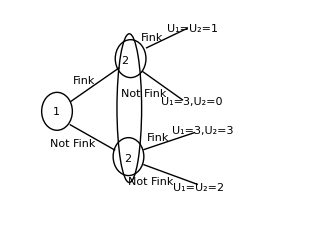

### Normal Form representation of the Prisoners’ Dilemma

□ | Fink | Not Fink
Fink | 1,1 | 3,0
Not Fink | 0,3 | 2,2

In the normal form representation we have a matrix where in each entry the first number is the U_1 and the second is U_2. Player on is shown on the left and player two is shown on the top.

### Thinking Strategically about the Prisoners Dilemma

At first glance of the table you might think that both will be silent because that results in the most total years of freedom, but you would most likely be wrong (assuming the player’s didn’t talk about it beforehand).

If you put yourself in one of the suspects shoes, however, you will know that regardless of what other player does it is always better for an individual to fink.

This was a rather easy game to solve because both players had strategies that were always better, but that will rarely be the case. So, for future games we need to develop a system that will allow us to solve less obvious games: enter John Nash and his equilibria.

## Nash Equilibrium

Nash Equilibrium: A strategy profile (s_1^*,s_2^*,....,s_n^*) such that, for each player 1 = 1,2,...,n, s_i^* is a best response to the other players’ equilibrium strategies.

A Nash equilibrium is stable in that even if players revealed their strategies to one another, no player would change their decisions.

### Applying Nash Equilibrium techniques to Prisoners’ Dilemma

To apply this it is usually helpful to have a normal form representation of the game.

Then what you do is say, If player 2 chooses x, what will player one do. You put a check in that box (here I underlined it). Then say if player two chooses y, what will player one do...so on and so on until you have tested all possibilities for all players in the game.

below is what this would look like in the Prisoners’ dilemma:

(Player 2 finks)/(□ | 1 ,1 | 3,0
□ | 0,3 | 2,2)(Player 2doesn't fink)/(1,1 | 3,0
0,3 | 2,2)(Player 1finks)/(1,1 | 3,0
0,3 | 2,2) (Player 1 doesn't fink)/(1,1 | 3,0
0,3 | 2,2) Final/(□ | Fink | Not Fink
Fink | 1,1 | 3,0
Not Fink | 0,3 | 2,2)

As you can see the final result is that both will fink because that box has the most check marks.

Dominant Strategy: A dominant strategy is a strategy S_i^*for player i that is a best response to all strategy profiles for other players.

If all players in a game have a dominant strategy the game is said to have a dominant strategy equilibrium.

The prisoners dilemma is an example of a dominant strategy Equilibrium game.

### Battle of the Sexes

The battle of the sexes is another classic example of a 2 player game where there are Nash Equilibria.

The story is that there is a wife (player 1) and a husband (player 2) who need to meet each other somewhere for a night out. They can either go see a chick flick or they can go to a football game. The husband would rather be at the ball game and wife would rather go to the movie, but it is more complicated than that. (the circle around the husbands choices imply that he is making his decision at the same time as the wife.)

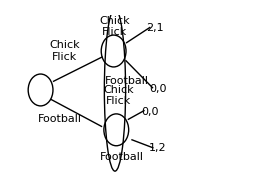
```mathematica
-Graphics-{{□, CF, FOOT}, {CF, 2,1, 0,0}, {FOOT, 0,0, 1,2}}
```

Now we will use our underlining (check mark) technique to find the Nash Equilibria ( NE)

Final/(□ | CF | FOOT
CF | 2,1 | 0,0
FOOT | 0,0 | 1,2)

Here you see that there are actually two NE’s, but no dominant strategies.

Because they are symmetric, it will be hard to tell which NE will actually play out. There is actually no purely mathematical way of answering the question.

## Mixed Strategies

So far we have only talked about pure strategies, or strategies in which a player makes a definite decision in the game. There can be mixed strategies, or strategies where a players move in the game is random. It may seem weird to study things where a players actions are determined by something random like a coin flip rather than their own rationale, but we will show that all games have NE in mixed strategies (even if they don’t in pure strategies).

Random strategies are actually quite common in real life. Think about studying for a test. There isn’t time or resources for a teacher to test on every word he said in class- so a student has to prepare for the random things he does test on. They happen in cards all the time when you have to make a decision before you know what the next card is going to be. It happens in sports where you don’t know what way your defender is going to make his move...

To mathematically display this idea we will say that all actions a player can perform are a set A = {a_i^1,a_i^2,...,a_i^M}, where the subscript is the player and the superscript is the number assigned to the action. A mixed strategy also has a probability distribution of the M actions, s_i = {σ_i^1,σ_i^2,... σ_i^M}, where the σ’s are number between 0 and 1 that represents the probability of player i playing action a_i^M. The probabilities in set s_i must sum to 1.

### Battle of the Sexes

In this game we have two players each with the same actions available to them, that is A_1=A_2={chick flick, football}. We can write a mixed strategy as a pair of probabilities (σ,1-σ), where σ is the probability that the player chooses a chick flick. If this strategy were (1/3,2/3) that player would have a 1/3 chance of choosing the chick flick and a 2/3 chance of choosing a football game.

All of the terms we have defined thus far are still valid, except that we need to define absolute payoff to be an expected payoff instead.

The wife’s strategy is (8/9,1/9) and the husbands is (1/5,4/5)

The wife’s expected payoff is U((8/9,1/9),(4/5,1/5)) = (8/9)(1/5)U_1(chick flick,chick flick)+(1/9)(1/5)U_1(football, chick flick) +(8/9)(4/5)U_1(chickflick, football) + (1/9)(4/5)U_2(football, football)=
(8/9)(1/5)2+(1/9)(1/5)0 +(8/9)(4/5)0 + (1/9)(4/5)U_2 1 = 16/45

WE could do the same thing for the husband, but it should be pretty clear now what is happening.

We will now show quickly the expected utility of the wife with variables instead of fractions:

u_1((w,1-w),(h,1-h)) = (w)(h)U_1(cf,cf) + (w) (1-h)U_1(cf, foot)+ (1-w)(h) U_1(foot, cf) + (1-w)(1-h)U_1(foot,foot) = w*h*2+w(1-h)*0+(1-w)*(h)*0+(1-w)*(11-h)*1 = 1-h-2+3wh

It is a pretty complicated process to examine a game and find mixed strategy NE, so we should remember the rule of thumb that all games generally have and odd number of total NE. So if we find an odd number of pure strategy NE’s, we have probably found them all. If there is only an even number of pure strategy NE’s we can probabilistically conclude that there is likely one more mixed strategy NE.

The book provided a long and rather convoluted way of solving mixed strategy games, but there is an easy way to. We just need to calculate the expected utility for one player making every decision  before them. These will be in terms of the other players probability strategies. Then we just say in order for player 1 to be indifferent those expected utilities must be the same. If that is the case we can solve for player two’s probability scheme that makes player one indifferent. Depending on which side of the fence player two is actually on we will be able to determine what the optimal strategy for player 1 is.

The main point of the last paragraph is that when you are solving for strictly mixed NE (no pure NE) players are only willing to randomize over actions among which he or she is indifferent, or that yield the same expected utility. The second main idea is that when you have figured out one player’s indifference condition, you necessarily “pin down” the other player’s mixed strategy.

## Existence

The reason we use NE so much is that there exists at least one for almost all games. That isn’t true for most other game theory techniques as we have already seen. In the battle of the sexes there are no dominant strategies , but there are 3 NE’s.

## Continuum of Actions

So far we have only been able to talk about games that have a discrete number of options, when in reality most games have an infinite continuum of choices. For example in imperfect competition firms can choose to set prices or set quantity. They aren’t limited to a multiple choice like selection of these strategies, but rather the entire continuum of real positive numbers.

### The Tragedy of the Commons

In this section we are going to present a method for solving games where there is a continuum of possible choices for each player. This can be broken down into a few steps as will be shown:

Write down the payoff for each player as a function of all players’ actions.

Now you will compute the First Order Conditions for each players payoff functions.

You can then solve each of these equations to find the reaction functions (Best response functions) for each player. You will get one equation for each player.

You now have a system of n unknowns and n equations that can be solved quite readily with linear algebra or graphical methods. (n is the number of players in the game).

The setup for our game is that we have two sheep-herders who need to share the public grazing ground between their two flocks. The issue is that the grounds are small and easily prone to over-grazing.

We will make this more mathematical by saying that q_i is the ith herder (there is only 1,2 in our version of the game) and that the per-sheep value of grazing on the commons is v(q_1,q_2) = 120-(q_1+q_2).

We can;t use matrix representation to present the normal form game, but the payoff functions are:

U_1(q_1,q_2) = q_1*v(q_1,q_2) = q_1(120-q_1-q_2)

U_2(q_1,q_2) = q_2*v(q_1,q_2) = q_2(120-q_1-q_2)

If we were to differentiate each of these functions with respect ot q_i, set them =0, and solve we would get q_1=q_2=60-1/2(60-q_i/2), where q_i represents the other persons choice. The end result is that both should choose accordingly so the sum adds up to 60 (30, 30  is most fair and probable).

As you might have been able to guess this isn’t what happens and both players graze more than is socially efficient resulting in overgrazing and lower marginal productivity.

## Sequential Games

There are other games where both players don’t make their move at the same time. In this situation it is really important to understand the dynamics of turn taking and timing. This game adds a different strategic component in that players who go second have the advantage of having seen the first player make their choice already.

### Sequential Battle of the Sexes

Now we will change the battle of the sexes game so that the wife and the husband don’t move at the same time, but the wife goes first. The strategy profile for the wife has not changed, but the one for the husband has expanded from 2^1 to 2^2. The best way to express them is using conditional format: S_h = {{CF|CF,CF|FOOT},{CF|CF,FOOT|FOOT},{FOOT|CF,CF|FOOT},{FOOT|CF,FOOT|CF}}. This is to be read as {husband’s choice | given wife’s choice}. As you can see he now has four strategies. One to pick CF every time, follow his wife, do the opposite as his wife, and FOOT every time. Below is the normal for representation of the game (note that I have omitted the “|” and the first in each pair is always |CF and the second is | FOOT):

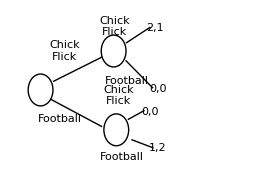
t□ | (CF,CF) | CF,FOOT) | (FOOT,CF) | (FOOT,FOOT)
CF | 2,1 | 2,1 | 0,0 | 0,0
FOOT | 0,0 | 1,2 | 0,0 | 1,2-Graphics-

Now that we have sequential games we can examine all three NE (both CF, both FOOT, or husband always FOOT). We can use what is called backward induction to determine which of the NE will hold up in reality. Before we do that we will qualitatively look at the husband always playing FOOT. He could make this kind of “threat”, but is it credible? If he does make the threat and the wife chooses FOOT she he will gain his maximum utility (2) and she will still gain one. Neither has a profitable deviation, so it is a NE. However it is an empty threat and shouldn’t be believed because if the wife “calls his bluff” and goes to the chick flick then he his best option is to go to the movie too. We will show this in an extensive form representation below where the dotted line is empty threat, the bold line is the expected path and the normal lines are not chosen. We start this process at the end of the game and ask ourselves if the husband gets to a particular node what will his choice be. We can then move backward and say knowing that, what is the wife’s best move?

-Graphics-

### Subgame Perfect Equilibrium

Game theory has a set of tools that allows you to solve sequential games by first eliminating empty threats and then working backwards. To do this we need to define some terms first

Subgame: A subgame is a part of the extensive form game that starts at any node and carries through to the end of the game.

Proper Subgame:  A proper subgame is a subgame hat starts at a node that is not connected another in an information set, this is easier to see. We will look at both sequential and non-sequential forms of the game and put a rectangle around each proper subgame.

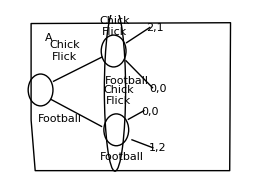
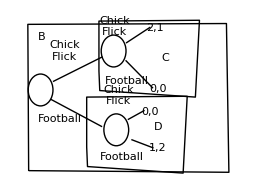

Ok so in the simultaneous form game (left) there is only one decision node that is not connected to another in the same information set; therefore only the game labeled A exists. In the sequential game, however, there is still that top level node for the wife (B) and then two distinct nodes for the husband (C,D) that are not connected by an information set.

Subgame Perfect Equilibrium: A subgame perfect equilibrium is a strategy profile that constitutes a NE for every proper subgame.

So, by definition the subgame perfect Equilibrium (SPE) is a NE. This means that to be a SPE you need to be a solution not only for the smaller proper subgames, but for the whole game because that is of it self a proper subgame. Let’s break this up one at a time for the battle of the sexes.

For subgame C the choice is ballet for the husband (1>0). For subgame D the choice is football for the husband (2>0). This reveals that the husband has only one strategy that can be part of the SPE: s_h:{CF|CF, FOOT|FOOT}.

### Backward induction

This is pretty much what we just did in the last section, we will now make it more clear by drawing arrows on the extensive form of the game to show expected paths at each node.

## Repeated Games (not on this exam, come back later if you have time, done up to pg. 263)

So far we have only talked about games where a player makes a choice once and the game is over. There are many real life applications where the same game is played over and over with different information or different circumstances.

### Finitely Repeated Games

Stage Game: A stage game is where you have the players set up and in each round they make a decision.

Trigger Strategies: If you have collusion among players (in the prinsoners' dilemma collusion would be agreeing not to fink) you will continue to play a non-Equilibrium solution that has higher payoffs for all players until someone deviates from colluded arrangement and that triggers a NE response by other players.

For a lot of stage games, playing them a finite number of times will not automatically increase the probability of cooperation. Think about it using  backward induction. You will start at the last proper subgame and in that situation the best response for each player will be the NE response. That will never change for any of the games that came before that.

Reinhard Selten made this observation and turned it into a theorem. The theorem says that in any stage game containing a NE, the SPE of each subgame is always to play the NE response for each player.

## Incomplete Information

So far we have only looked at games where the setup included each player knowing exactly what the strategies and payoffs were for all other players. This is not realistic. In order to look at games with imperfect information we will need to unite the game theory topics from this chapter with the uncertainty and information ideas from the previous chapter.

One tool that is used often in probability theory to make good guesses about unknown information is Bayes’ rule.

## Simultaneous Bayesian Games (Again, not on the exam so come back, up to pg 270)

The setup for this game is that there are two players and player one has more information than does player 2. (he=player 1, she =player 2).

□ | L | R
U | t,2 | 0,0
D | 2,0 | 2,4, where t is known only to player one and has 1/2 probability of being 6 and 1/2 probability of being 0.

### Player types and beliefs

To understand these games we need some vocab. A player type in our example is the value of t that is known only to player 1. In this case s_1(t) is a function of t, while s_2 is unconditional. In normal games, a player’s payoffs depend on the strategies employed by the players, in Bayesian games the player’s type also comes into play. We can now write the expected utility expressions:

u_1(s_1(t),s_2,t), u_2(s_2,s_1(t),t) (note that t is in u_2's profile twice because it directly affects him and it indirectly does through 1's strategy)

### Bayesian-Nash equilibrium

## Signaling Games

## Experimental Games

## Evolutionary Games and Learning

13

General Equilibrium and Welfare

## Perfectly Competitive Price System

Perfectly Competitive Price System: In this system there are  a large number of homogeneous goods and the market for each of these goods is determined from the supply and demand forces for them. Each good therefore has an equilibrium price, the price that allows the market to clear, or the price at which quantity demanded is equal to quantity supplied.

### The Law of one price

This law is a result of the fact that we have zero transaction costs and perfect information. These two assumptions mean that suppliers and demands are all subject to the market price and no individual supplier or consumer can alter the price.

### Behavioral Assumptions

This model makes some Assumptions about people and firms:

There are a Large number of consumers for every good. Each person takes all the prices as given and adjusts their own consumption to maximize their utility subject to their budget constraint (or income). People may also  be suppliers of labor and their decisions regarding work also take prices (wage) as given.

There are a large number of firms producing every good and each of them produces only a small part of the total market output for that good. A firm is always trying to maximize profits when they make input and output choices. They take all input and output prices as given.

## A simple graphical model of General Equilibrium with two goods.

### The Edgeworth box diagram for production.

To construct the edgeworth box we have the horizontal axis representing the total labor in the market, while the Vertical represents to total capital in the market. We also call the bottom left corner the 0_x point, which represents no production of x. A similar idea for y is true, but that point is the top right corner. With this setup any point in the box will be a possible allocation of labor and capital in the production of x and y.  This is shown in the first figure.

If we want the allocation to be both possible and efficient we must draw in the isoquants for x and y and then draw a line from 0_x to 0_ythat passes through all the isoquants. This is shown in the 2ndfigure.

-Graphics-

-Graphics-

### The Production Possibilities Frontier.

The Production Possibility Frontier: This shows the alternative combinations of two outputs that can be produced with fixed quantities of inputs if those inputs are used efficiently.

-Graphics-

### The Rate of product Transformation

The slope of the PPF represents how x output can be substituted for y output when all resources are held constant.

The Rate of Product Transformation (RPT): The RPT between two outputs is the negative of the slope of the PPF for those. It represents the idea of opportunity cost.

RPT = - (∂y)/(∂x)

If we let the total cost for suppliers be C(x,y) a function of x and y we will have the following when all inputs are fixed in supply.

∂C = (∂C)/(∂x)∂x + (∂C)/(∂y)∂y

Upon rearranging and solving for - (∂y)/(∂x)we get:

RPT = - (∂y)/(∂x) = (∂C/∂x)/(∂C/∂y) = MC_x/MC_y

### The shape of the PPF

The PPF is usually concave to the origin. This is due to a few factors

Specialized inputs: This is a very rational idea that some inputs are better suited for development of one good over another. Thus, those would be the last ones to be reallocated to the other good and the slope gets pretty steep as they start to be moved.

Differing Factor Intensities: This is the idea that not all goods  use the same amount of specific inputs. Similar to specialized inputs, but a bit more general.

#### Example: Concavity of the PPF

We will often be given production functions for goods x  (10) and y (11)  in terms of the amount of labor spend on x and the amount of labor spent on y. We will also be given a total labor constraint (12) that says total labor to be spent on producing x and y is some number. To obtain the PPF (13) we simply need to solve equations 1 and 2 for x l_x and l_xand plug them in.

x = f(l_x) = √l_x

y = f(l_y) = √l_y

l_x+l_y = 100

PPF: x^2+y^2==100

RPT = -(∂y)/(∂x) = (- (-2x))/(2y)= x/y

Another idea is that you might have production functions in terms of capital and labor

x = f(k_x.l_x) = √(k_x*l_x)

(y = f(k_y,l_y) = k_y^0.25*l_y^0.75

k_x+k_y=100, l_x+l_y=100

RTS_x = k_x/l_x = κ_x, RTS_y = (3 k_y)/l_y = 3 κ_y

-Graphics-

In the Figure above we have a price ratio given by p_x/p_y (as shown by the the price line C).With that price ratio, firms will choose to produce at the point (x_1,y_1). At this same price ratio, consumers will demand consumption at (x_1', y_1'). These opposing forces will make sure that price adjusts to where we have the price ratio (p_x/p_y) = -RPT = MRS. This is shown on the figure as point (x^*,y^*).

## Welfare Economics

Pareto Efficient Allocation: An allocation of resources is Pareto efficient if it is impossible to make one person better off without making someone else worse off.

Production Efficiency: An allocation of resources is efficient in production (technically efficient) if no reallocation of goods would permit more of one good to be produced without reducing the output of another good.

It is not possible to reach Pareto efficiency if we are not experiencing production efficiency. Production efficiency, however, only deals with suppliers acting properly. to ensure that demands to also you need to bring them into the picture by saying that if the RPT has to equal the price ratio for all firms, so does the MRS thus:

(- (∂y)/(∂x)= (∂C/∂))/(∂C/∂y)= RPT = MRS = (∂U/∂x)/(∂U/∂y)=- (∂y)/(∂x) ) = p_x/p_y

## Competitive Prices and Efficiency: The First Theorem of Welfare Economics

The idea behind Pareto efficiency is actually really simple. You need the rate of trade-off between any two goods, x and y for example, to be equal for all economic participants. In a perfectly competitive market economy an easy measure of this is the price ratio.

The First Theorem of Welfare Economics:  All agents in a market must face the same prices. As agents maximize their benefit (Utility for consumers and π for suppliers) this will force all trade-off rates to be equalized and thereby producing a Pareto efficient result.

## Distribution and the Second Theorem of Welfare Economics

Contract Curve: If you were to draw an edgeworth box for two individuals in a market and map out their particular indifference curves, the points of tangent of the isoquants, along with the 0 points for both of them would be called the contract curve. The contract curve represents all possible efficient allocations of goods between these two people.

The Second Theorem of Welfare Economics: The theorem states that any desired distribution of welfare among the individuals in an economy can be achieved in an efficient manner through competitive pricing if initial endowments are adjusted appropriately. This cuts a defining line between efficiency issues and equality issues. Another definition says “Any Pareto efficient allocation of goods can be sustained by competitive pricing”. (This means the status quo can be maintained forever).

14

Monopoly

## Barriers To entry

Monopoly: A monopoly is a single firm that serves an entire market. This firm then faces the market demand curve for its output decisions. A monopoly can usually choose either the price at which goods will be sold in the market or the quantity of goods it will supply, but it can’t choose both.

### Technical Barriers to entry

The nature of the market might be such that the production of the good requires substantial fixed costs, but that the firm will then enjoy decreasing marginal and average costs. This is known as a natural monopoly simply because it makes the most economic sense to have one large firm incurring large fixed costs than a lot of smaller firms incurring large fixed costs.

### Legal Barriers to Entry

Sometimes monopolies are created by a law rather than the natural economic forces behind the market. The most common example of this when a copyright or patent comes to protect a certain technology. The other main type of legally created monopolies are those of a “franchise”. This means that the government has given one firm the right to control a market (utilities are common example), not without restrictions of course.

### Creation of Barriers to entry

Sometimes a firm finds itself in a monopolistic position and they will act to make sure things stay that way and they don’t lose their market power. Some things they might do  are buy up all the natural resources needed to compete in a market, or they might have pricing strategies.

## Profit Maximization an Output Choice

To maximize profits a monopoly will choose to produce that Output level for which marginal revenue (MR) is equal to marginal cost (MC)!! Because the monopolist faces a downward sloping demand curve, this will result in price being higher than marginal cost and marginal revenue.

MR = MC

Monopoly Rents: A monopolistic market is resistant to additional entry by outsider firms so the monopolist can earn long run profits. These are commonly called monopolistic rents.

It should be noted that a monopolist doesn’t actually have a supply curve.

## Monopoly and resource Allocation (COME BACK FOR TEST 2)

Because a monopolist produces where MC and MR are equal to each other, but less than price Price no longer gives us accurate information regarding the underlying costs in the market.

Even though a lot of the loss consumers experience goes to the monopolist in form of profits π, there is still a pretty big DWL Because of the mis-allocation of input resources and the market power the monopolist has in being able to fix Q_s or P_d.

Below are some equations to help you understand the welfare situation with a monopoly.

CS = ∫_P_0^∞ Q(P)ⅆP

## Price Discrimination (COME BACK FOR TEST 2)

Price Discrimination: A monopolist is engaging in price discrimination if they are selling identical goods to different consumers at different prices.

The idea behind price discrimination is that a monopoly will be able to increase profits if they can somehow recover more of the CS or the DWL.

In theory it will be impossible for a monopolist to practice price discrimination if its customers have any type of ability to practice arbitrage. That if one consumer buys a good at a low price and then turns around and sells it to another customer at a higher price, pocketing the difference.

### First Degree Price Discrimination

First Degree Price Discrimination: This is also known as perfect price discrimination and happens when a monopolist knows exactly what every customer is wiling to pay for a good and then sells this good to them at that price.

The result of this is that the monopolist will capture ALL of the CS and retain it as π.

### Third Degree Price Discrimination through Market Separation

Third Degree price discrimination: this is when the monopolist doesn’t know everything about every customer, but knows enough to separate the customers into different groups and then charge groups a price for the goods.

This results in the monopolist being able to extract chunks of CS away from the consumer as π

## MORE MONOPOLY STUFF TO BE COVERED IN PREP FOR TEST 2!

15

Imperfect Competition

## Short-Run Decisions; Pricing and Output

We will now study what happens in a market where there are only a finite, small number of firms. There are a few different models that try to predict how pricing and production will play out and we will examine the most popular ones in this Chapter. Among them are the Bertrand Model, The Cournot Model, and other models with partial or complete collusion among players in this oligopoly game.

## Bertrand Model

This was named after a guy named Bertrand and in the model there are two identical firms labeled 1,2 that produce identical products at a constant marginal (and therefore average) cost c. The firms will choose their prices p_1 and p_1 at the same time and all sales will go to the firm with the lower price. We know that if p_1=p_2 they exactly split sales. D(p) is the market demand.

### Nash Equilibrium of the Bertrand game

We cannot use methods developed in chapter 8 to solve this game because the profit functions (π) and price functions are not actually functions. Firms will simply set prices initially and then adjust them little by little to try and get a bit more profit. For that reason we will not be able to mathematically derive a NE, so we will guess that the only NE is that p_1^*=p_2^* =c.(this means that the proposed solution is a NE and there doesn’t exist any other NE)

We can verify that the proposed solution is indeed an NE by showing that there is no profitable deviation for either firm to go away from that price. If you are there, someone could try to raise their price and get some economic profit, but doing so would cause all customers to go to the other firm and sales would be zero. This is not profitable. The other option is that you could put prices just below the current level and thereby attract all customers to your firm. Doing this would mean you are selling at a price that is below marginal cost and doing so could cause negative profits and therefore isn’t a good deviation either. Thus we have just done a qualitative proof that the equilibrium presented above is indeed a NE.

To show that it is the only pure strategy NE we simply try any other point. If prices were anything else they would have to be above c. In this situation it is profitable for neither firm to raise prices (give up all sales), but it is profitable for both firms to cut prices (taking all the sales) and we would be in this constant spiral where one firm under cuts the other until finally we reach a point where neither firm is willing to lower their prices any more. This happens with p=c and we have arrived at our NE as discussed above.

### Bertrand Paradox

We have just discovered that the Bertrand solution to the two firm problem is identical to the competitive situation where you have infinite firms. Price is at marginal cost and neither firm makes a profit. This is called the Bertrand paradox because you wouldn’t expect competition between just two firms to be so hard, but it is. This was a general conclusion in that it wasn’t tied to specific demand or cost functions, but not general in that if you change any of the underlying assumptions (firms set quantity instead of price [Cournot game], cost functions are different, there is slight differentiation among your products, there are close substitutes to the products...) you no longer get the competitive result.

It is trivial to extend this model to more than two firms. In any case where n > 1 you will have perfect competition because firms will continue to undercut each other until they reach p=c.

## Cournot Model

The Cournot model is similar to the Bertrand model, but the difference this time is that we will have our identical firms choose quantities instead of prices and let the demand curve set the price. This is a fairly simple change in the setup of our problem, but it will have huge implications on the results. Price will end up above marginal cost and firms will be making positive economic profits. We should also note that the simple change in setting quantity instead of price does change the firms’ profits in an oligopoly, but with a monopoly it didn’t matter at all whether they set q or p.

We will start with the general form of the game with n firms who choose their output q_i, i (1,n). The total industry output is Q = ∑_(i=1)^n q_i and a market price P(q). The profit for each firm is:

π_i = P(Q)q_i-C_i(q_i)

### Nash Equilibrium of the Cournot Game

Unlike the Bertrand game, the Cournot game has differentiable profit functions so we can therefore maximize the profit of each firm based on quantity and solve for each firm’s best response to the other firms.

(∂π_i)/(∂q_i) = (MR)-(MC) = (P(Q) + P'(Q)q_i)- (C_i'(q_i))= 0

We get from the above equation the all-to-familiar result that MR=MC for a profit maximizing firm. In this case, however, you have MC = P + “wedge term” (P'(Q)*q_i). This means that price must be higher than marginal cost by a factor equal to the wedge term for each firm. In this case if a firm decides to produce one more unit that q_i it will cause price to drop by a factor equal to P'(Q) leading to a total loss in revenue of P'(Q)q_i. (this is the total effect because the one additional unit lowers the price for all units to be sold, not just that one).

We will go over an example with 2 firms and simple cost/demand functions. We will show the Bertrand, cournot, and perfect cartel solutions and provide some comparative statics between the two of them. The setup of this problem is that there are two springs with a large supply of water and the owners need to decide how much to provide the market. A firm’s cost of pumping and distributing the water to the market is equal to C_1=C_2 = c*q_(i.). This implies that marginal and average costs are constant. The inverse demand for the water is P(Q) = a-Q, where a is the demand intercept and Q = q_1+q_2 = total water supplied by owners.

The Bertrand model will say that both of the firms will price at marginal cost. The market price is P* = c, total output is Q = a-c, firm profit π=0, and total profit in the market is also zero. For the Bertrand model to produce anything we have to have a >c, which we assume is true for the entirety of the problem.

The Cournot Model requires that we set up profit functions for individual firms.

π_i = P(Q)q_i-cq_i = (a-q_1-q_2-c)q_i

Solving first order conditions yields the following reaction (best response) functions:

q_1 = (a-q_2-c)/2, q_2 = (a-q_1-c)/2→ q_1^* = q_2^* = (a-c)/3

Perfect Cartel: The perfect cartel case implies that joint profits are maximized, or that the firms act together as if they were a monopoly and split the profits evenly. Fro that reason I will not talk about them here, see the monopoly section for an explanation of how this is done.

Comparison. Moving from Bertrand to Cournot to perfect cartel we see that profits per firm go from zero to the theoretical maximum.

### Varying number of Cournot Firms

The Cournot model is very effective because as we change n from 1 to ∞ we can see the whole spectrum of possibilities covering the perfect competition all the way to monopoly.

If you say that all the firms have same cost and profit functions you will say that q_1 = Q/n. Substituting this into the equation numbered 2 above you will get the wedge term to be P’(Q)*Q/n, which shows that the price above marginal cost will diminish as n grows and eventually reach zero when n is very large.

If we extend our example from above to n different firms we will get the following equations

π_i = = P(Q)q_i-cq_i = (a-Q-c)q_i = (a-q_i-Q_-i-c)q_i

Where Q_-i is the output for all firms besides firm i.

(∂π_i)/(∂q_i) = a-2 q_i - Q_-i-c=0

We can now recognize that all firms will have exactly the same set of conditions because they have identical cost, profit, and demand functions they are facing. Making this theoretical connection allows us to jump to the answer fairly quickly

(Q^*)_-i = Q^*-q_i^* = nq_i^*-q_i^* - (n-1)q_i^*

a - 2 q_i^*-(n-1)q_i^*-c = 0

Q^* = nq_i^* = (n/(n+1)) (a-c)

P^* = a-Q^* = (1/(n+1))a+(n/(n+1))c

### Prices or Quantities?

It may seem surprising that looking at setting price versus quantity would make such a big difference in the market. Looking a little deeper though you can see that undercutting price takes away the entire market from other suppliers so you would expect that game to be tougher. Quantity, on the other hand, changes the price of all the goods, but doesn’t have the dramatic effect of wiping out all of the other firms revenues.

A blatant disadvantage of the Bertrand model is that it makes the abrupt jump from monopoly to perfect competition with a move from 1 to 2 firms.

A big disadvantage in the Cournot model is that in real life firms set prices rather than quantities.

## Capacity Constraints

In order for the Bertrand model to produce the expected results you would have to have firms with unlimited capacities. If you think about it, as soon as one firm lowers their prices the demand for their good more than doubles (picks up equal quantity from other firm’s previous demand, plus marginal buyers at lower price). This is not realistic to think that a firm will have the capacity to service such an abrupt change in demand.

If you make the Bertrand situation into a two stage game where in the first stage you build facility to generate capacity and in the second stage you set prices you know that in the second stage you don’t have the ability to provide more to the market than what your buildings can store from stage one. This will lead to the exact same solution as the Cournot model because essentially firms are choosing quantity when they build their storage facilities to have a certain maximum capacity.

## Product Differentiation

Another solution for avoiding the Bertrand Paradox is to get rid of the assumption that all goods are exactly alike. This is particularly realistic in real world markets.

### Meaning of “the market”

The possibility of product differentiation makes our idea of a market kinda fuzzy. It is no longer where people go to by one of any number of identical goods. People used to shop only at places where the price was lowest, now they have more to think about when they decide from whom they will buy their goods.

Now we have to take the market as a place where very similar differentiated products are all sold at relatively equal prices.

### Bertrand competition with differentiated products

There are many different ways in which products can be differentiated. It could be on color, taste, size, location, ect...

If we do have a series of differentiated products we will have q_i(p_i,P_-i,Q_-i,A_-i) where p is the good’s price, P and Q are price and quantity for all other goods in the market and A is a list of all other firms’ products attributes besides firm i’s. The total cost function then becomes C_i(q_i,a_a) and profit is:

π_i = p_i q_i-C_i(q_i a_i)

To solve this kind of problem you would just need to differentiate each of the π’s with respect to the q’s, set them equal to 0 and solve.

#### Hotelling’s Beach (COME BACK LATER AND DO EXAMPLE 15.5)

One popular example of differentiated Bertrand solutions is Hotelling’s beach. The setup is that you have two identical ice cream carts on the beach that are spread out at positions a and b. The demand for each ice cream cart is A and B. The ice cream is identical except for the opportunity cost associated with having to walk a certain distance to get your ice cream (we assume that people don’t like to walk so it is bad to go far). The cost for each buyer of a cone is td^2 where t is the time is takes to walk back to your spot on the beach and d is the distance walked.

I really don’t have time to do this example right now.

### Consumer search and price dispersion

Another way to get rid of the Bertrand paradox is to say that consumers do not know the price of the good they want at all locations. This is a reasonable assumption because in order to know the price of the good everywhere you have to do some pretty good searching and that can cost a lot of time.

## Tacit Collusion

There is a difference between tacit collusion and an explicit cartel. The cartel is established by legal documents and has specific penalties laid out if you break your commitments. A tacit collusion on the other hand, can only be enforced through punishments internal to the market (that means only those punishments that can be generated by other players playing the SPE over and again). Cartels are usually illegal to a Tacit collusion is the only way available to most firms to fix prices above marginal cost.

### Finitely Repeated Games

Repeating the game a finite number of times will not change the outcome. We learned this from Selten’s theorem in Chapter 2.

### Infinitely Repeated Games

If you switch to a game with infinite periods you now have the folk theorem coming into play. This theorem says that any feasible equilibrium can be sustained for an infinite amount of time as long as the discount factor δ is close to unity (1). The discount factor δ is a rough measure of how patient players are. The monopoly outcome is a feasible result according to the folk theorem as long as δ is close enough to 1.

If we start at the monopoly price and monopoly profit in the market and assume all firms are playing the grim trigger strategy (maintain monopoly until someone undercuts price and then move to SPE) we will easily be able to see that no firm will ever want to undercut his competition because doing so would decrease his profits (assuming he really believed they would hold true to their promise to play the SPE response).

## Longer-Run Decision: Investment, Entry, and Exit

So far we have only talked about firms setting price or quantity, but shift to the long run and you have a whole new set of strategic variables. Firms now need to decide to update their products model, to invest in expensive capital, to move manufacturing plants closer to consumers to cut down transportation cost. ect...

### Flexibility versus Commitment

There is a question as to whether it is better for a firm to be able to easily reverse its choices or if it is better for them not to be able to, thus forcing them to commit. For a monopoly the obvious answer is that flexibility is good. If you are the only firm servicing a particular market you need to be able to customize your products to the needs and specifications of the consumer if you want to capture as much of the market as possible.

For a competitive firm, or even one in oligopoly it is harder to tell. Obviously there are some business decisions that need to be changed or modified, but sometimes this can lead to a wandering firm without direction and therefore without a dedicated client base. When a firm changes a product they will enjoy a “first-move” advantage that allows them to get a customer pool before other firms ever have a chance to make an impact in the market. This will allow you to stand firm in what you do and hold that advantage (a loyal customer base) for a long time rather than revert to something else when another firm enters the specific market.

### Sunk Costs

Sunk Cost:  A sunk cost is one that is in the past and you can’t reverse it or resell it. Think of non-refundable airline tickets or the money spent at the movies last weekend.

### First-mover advantage in the Stakelberg model

The best and easiest place for us to take a look at the first-mover advantage is in a model called the Stakelberg model, named after the man who first analyzed it. The model is very similar to the model presented by Cournot, except that instead of both firms choosing output at the exact same time, one firm gets to go before the other one. We call the first firm to make production decisions the leader and the other firm is the follower.

In this situation the game is best solved using backward induction to arrive at the SPE. We do this by saying what will the follower choose to produce (q_2) that will maximize its own profit, taking the leader’s output(q_1) as a given. This will result in the same best result function calculated from the first order conditions in the Cournot model. We call this BR_2(q_1).

Then you will turn to the leader’s output choice. The leader knows its decisions affect the other firms so they take that into account when trying to maximize their profits. Their profit function becomes:

π_1 = P(q_1+BR_2(q_1))q_1-C_1(q_1)

(∂π_1)/(∂q_1) = P(Q)+P'(Q)q_1+[[P'(Q)(BR')_2(q_1)q_1]]-C'(q_1)=0

This is the exact same as what was computed in the Cournot model, except for the addition of the term in [[ ]] which I will call s, the strategic factor. This factor will cause firm one to produce more than they normally would, which reduced firm 2’s output and raises price.

### Contrast with price leadership

In the game just presented the leader uses what is called the “top dog” strategy, where the aggressively overproduce to force the follower to scale back its production.

One strange thing is that it is not always true that in this sequential game the leader gets profits greater than or equal to the Cournot solution while the follower gets less. It can be true that they both have increased profits. There hasn’t been a general way to say this presented to me, but it just requires that you solve the stakelberg game and the cournot game for the same situation and compare the profits for each firm under each game. (Note that it is true that the leader is never harmed by going first. It is completely in their control to get at least as good as the Cournot outcome). This is called a “Puppy dog” strategy.

## Strategic Entry Deterrence

In the last section we saw that the first mover effect increased the profits of the leader firm compared to the follower firm or the Cournot firm. In this section we will see what the leader firm can do to one up that result by causing all other firms to exit the market, or never enter in the first place.

This would be accomplished by the leader firm if they produced at a level so high that the price fell enough that firm two no longer found it profitable to be in the market. This could be better or worse for the leader depending on the slope of the second player’s BR function.  There are two principles we learned in the last two sections:

Entry deterrence is always accomplished by a “top dog” strategy whether the competition is in quantity fixing or price fixing, or (more generally), whether best-response functions slope up or down. The first mover simply wants to create a market where no one else can afford to operate.

If firm 1 is ok with other firms in the market he will play a “puppy dog” strategy or “top dog” strategy depending on the nature of the competition- in particular the slope of the BR functions.

## Signaling

The previous sections talked about how the first-mover advantage can be won by a leader firm in a game where commitment is required. Now we will talk about a game where the followers may not have all the information about the market and they will try to infer things about the market by watching the leader’s decisions. The leader can send tricky signals to the follower if he suspects this is going on. This type of benefit is more valuable in markets where the benefit of being able to commit early is not really there (perhaps because start up costs are very low and reversible in this market).

### Entry-deterrence model

We will set up this model by saying we have two firms and at first only one of them is active in the market. They have a particular marginal cost function that is not known to the second firm, but has a probability of being high (Pr(H) and a probability of being low Pr(L) = 1-Pr(H)). The second firm sits out the first period, observes the pricing of the first firm and then decides if they want to participate in the second period. If they do decide to enter they sink some start up costs K_2 and get to know the first firms prices as they compete in a 2 firm duopoly. If firm two doesn’t enter they get 0 profits and firm one continues as a monopolist.

Firm two will earn more money in a market where prices are high because they will be able to cover more of their costs. So they observe the pricing strategy of firm one during the first period.

We are saying that D_i^t is the Duopoly profit for firm i if firm 1 is of type H or L. We know that D_2^L<K_2<D_2^H. This means that firm two only wants to enter if costs are high for firm 1 because if not they won’t be able to recover their fixed costs.

We are also making a simplifying assumption that if prices for firm 1 were low in the first period that also means their costs were low. It is only when prices were high that there is a chance for firm one to decide if it wants to price high or low.

In the model R represents a loss incurred by firm one by not being able to charge its period 1 optimum during period 1 because it was trying to send false information to firm 2. The payoffs above are all total payoff after two periods (total profits in that time).

### Separating equilibrium

The only way pricing differently to deter entry by firm 2 is unprofitable for firm 1 is if M_1^H+D_1^H≥ 2 M_1^H-R or R ≥ M_1^H - D_1^H. In words this is saying that the loss from distorting prices from the monopoly optimum is more than the difference in the monopoly and duopoly profits.

### Predatory Pricing

Predatory Pricing: Predatory pricing is possible when there is incomplete information and happens when a firm charges artificially low prices to deter other firms from entering the market.

Predatory pricing is illegal. It is against anti trust laws.

The most famous example is with John D. Rockefeller in the 1920’s trying to do that with standard oil.

## How Many Firms Enter?

In this section we will talk about how many firms are likely to participate in a market. We will simplify the model we have been talking about and say that all firms must make their entry decisions at the same time.

### Barriers to entry

In order for a market to be oligopolies with a finite number of firms, instead of competitive with ∞ firms, there must be barriers to entry into the market.

In the monopoly section we talked about things like search costs and stuff. The new ideas we will introduce are consumer search costs in not being able to find new firms with better prices, product differentiation leading to brand loyalty, and other things like high capacity, or predatory pricing.

### Long- Run Equilibrium

The setup for this game is that we will have to figure out how many, n, firms will enter a market. We will collapse all earnings for a firm into the PV and call it g. There are two assumptions that must hold throughout our analysis. First that for the n firms g(n^*) ≥ K, and g(n^*+1) ≤ K, where K is the startup cost for each firm in the market.

### Feedback effect

You also have to consider the fact that the more profitable a market, the more firms will want to enter, leading to more competition and less profits. This is easily seen in the different results obtained using Cournot and Bertrand models. In Bertrand if firms were allowed to make rational entry decisions only one firm would enter the market because 2 firms would cause profits to be zero and neither could make up their sunk costs. In Cournot, on the other hand, they would both enter. So it is a tricky subject to talk about what will happen as more firms enter a market or even before that as profits turn up in a market.

## Innovation

There was a question as to whether a monopolistic market or a perfectly competitive one would produce more innovation. If the monopoly is true then long run total social welfare will be higher if you don’t break the monopoly up. If the other is true both short and long run total social welfare is higher if you do break it up so the answer is tough.

There are differing ideas, one of which is that

### Monopoly on Innovation

If you suppose there is only one firm in the market that has an idea for a new product. How much would they be willing to spend to develop and distribute this product? The answer is that they are willing to spend up to the amount of extra profit they stand to gain by coming up with the product. In the Bertrand model, if you have one firm the monopolist is willing to spend a lot to do it, if there are 2 or more firms profits are zero and therefore the firm will be willing to spend zero dollars trying to come up with this new product. There is a general principle behind this idea that can be applied to more than just the Bertrand model and it is called the dissipation effect:

Dissipation Effect:  The dissipation is the fact that the more competition you have the more ways the profit has to be split and the less any one entity will be willing to spend developing some new innovation.

This effect is part of the motivation behind the patent system.

The opposite can also be true. Say the idea is out there for the public to wrestle with. If there is a firm not yet in the market, but if they develop a new product they will be part of a duopoly with an existing firm, they will be willing to spend up to the profits to be gained by a duopolies. On the other hand the firm already in the market would not be willing to spend anything at all since they are already enjoying monopoly profits. This is called the replacement effect

Replacement EffectL: The replacement effect is that firms gain less incremental profit, and thus have less incentive to innovate, if the new product replaces an existing product already making a profit than if the firm is a new entrant in the market.

### Competition for Innovation

New firms are not always more innovative than existing firms, the dissipation effect can outweigh the replacement effect. Assume that more than one firm has an idea for a new product. These firms will compete to see who can innovate the product first and best in order to get a sustained first-mover advantage. The difference in this variation on the model is that if firm 2 doesn’t innovate the product it isn’t left behind, rather firm 1 finishes the job.

16

Labor Markets (not comprehensive for chapter!)

## Allocation of time

All people face the trade off between work and play. We will present a model that has those as two goods in a utility maximization problem.

In the below equations U(l,h) is utility based on labor hours (l) and play hours (h). Income is given by c.

l +h = 24

c = awl = w( 24-h)

c+ wh = 24w.

## Monopsony in the Labor Market

Monopsony: There is only one buyer in the labor market ( only one firm willing to hire workers). This means that the firm will either be able to control how much labor it will buy, Q, or what to pay for that labor, w.

Marginal Input Expense: The marginal expense(ME) associated with any input is the increase in total costs of the input that results from hiring one more unit . If the firm faces an upward sloping supply curve (which they always do) this will be higher than the price of the input.

ME_L = (∂wL)/(∂L) = w + L (∂w)/(∂L)

To maximize profits the monopsonist must go until the following condition is met (f(l) is production as a function of labor)

w + L (∂w)/(∂L)=ME_L = MRP_L = P* (∂f)/(∂l)

17

Capital and Time

## Capital and the Rate of Return

Capital: The capital stock of an economy is the sum total of all machines, building, ans other reproducible resources in existence at some point in time. They are part of the economy’s past outputs that were not consumed, but set aside to assist in production for the future.

### Capital and the rate of return.

Single Period Rate of Return: The Single Period Rate of return (r_1)on an investment is the extra consumption provided in period  2 (x) as a fraction of the consummation forgone in period 1 (s). That is

r_1= (x-s)/s=x/s-1

Perpetual Rate of Return: r_∞is the permanent increment to future consumption (y) expressed as a fraction of the initial consumption forgone(s):

r_∞= y/s

## Determining the Rate of Return

### Rate of Return and price of future goods

Price of Future Goods: The relative price of future goods (p_1)is the quantity of present goods (c_o) that must be foregone to increase future consumption (c_1) by one unit:

p_1=Δc_0/Δc_1= 1/(1+r)

### Demand for future goods

We now have the problem of needing to develop a market for current period and future goods. This is done using the same Utility maximization techniques learned earlier. We must decide how much of our current wealth (W) we want to spend on goods today and how much of it we want to save for future consumption. In this case W = c_0+p_1 c_1 becomes our budget constraint.

p_1, because of its definition, will always move in the opposite direction of the rate of return. This makes sense because if the rate of return grows really high it makes more sense to save today and spend tomorrow, thus decreasing the relative price of tomorrow’s goods.

### Utility Maximization

It should be noted that in the below example there is something called the “rate of time preference” that is equal to 1/(1+δ) where δ  > 0.

#### Example: Inter-temporal Impatience

W = = c_0+p_1 c_1= c_0+c_1/(1+r)

U(c_0,c_1) = U(c_0)+ 1/(1+δ)U(c_1)

L =U(c_0,c_1) + λ [W - c_0-c_1 p_1]

(∂L)/(∂c_0)= U'(c_0) - λ =0

(∂L)/(∂c_1) = u'(c_1) 1/(1+δ) - λ/(1+r) = 0

(∂L)/(∂λ) = W = c_0- c_1/(1+r)=0

( ∂L/∂c_0)/(∂L/∂c_1) → U'(c_0) = (1+r)/(1+δ)U'(c_1

Consumption Smoothing: We know that all real Utility functions exhibit diminishing marginal utility and for this reason individuals will seek to equalize their consumption across all periods. This is called Consumption smoothing.

### Effects in Changes of r

It is easy to see from this figure that if p_1falls (that is r rises) both income and substitution effects will cause c_1to rise, Except if somehow c_1is an inferior good.

On the other hand, a change (say decrease) in p_1has an ambiguous effect on c_0. The substitution effect says the individual should substitute c_1 for c_0, but the income effect says total wealth has gone up and now the individual should increase consumption of both goods.

-Graphics-

## The Firm’s Demand for Capital

### Determining the rental rate of capital

Assume that a company rents machinery. What costs do they face when it comes to owning this machinery? There are two: depreciation of the good (p*d), and two the opportunity cost of having your funds tied up in illiquid goods (p*r). These can be represented by p*d + p*r = p(d+r)

ν = p(r+d)

### The Ownership of Machines

If the firm doesn’t rent their capital, but in fact owns it they face a different set of costs and therefore a different model for representing them. We should be aware that there the idea of stock and flow for a firm. The flow would be something like capital services, which are the number of machine hours needed to reach a certain output (kinda like labor hours in a labor market). The stock part, on the other hand, is more like the actual number or stock of machines needed to get the job done.

Demand for Capital: The profit maximizing production firm in a perfectly compete market will hire additional capital input t=up to the point at which its marginal revenue product for capital (MRP_k) is equal to the market rental rate for capital ν.

MRP_k = ν = p(r+d)

## Time Value of Money (Present Discounted Value)

When a firm buys capital we should really think of that as a firm buying a source of revenue for the future. To decide if it is a worthwhile investment to buy the machine, a firm must decide if the net present value of all future cash flows is more than the current market price for the good. If it is then the firm will come out of the transaction on top and it is profitable to buy the machine.

For analysis of this situation we will say that the good will be useful for n years, produce revenues of R_ifor every year i, and that r is the current interest rate that is expected to remain constant for the lifetime of the good. We can then say that the Net present value or Present Discounted Value of the machine is:

PV= PDV = ∑_(i=1)^n R_i/(1+r)^i

#### Example 17.2: Cutting down a tree

Imagine you are a forester who must decide when to cut down a growing tree and sell the proceeds. We will assume we know the value of the tree at any given time as given by the function f(t) [where f’(t) >o, f’’(t) < 0]. WE will also assume that l dollars were invested initially as payments to the workers who planted the tree along with the cost of the seeds and the market interest rate is r.

PDV(T) = e^-rt f(t) - l.

(∂PVD)/(∂t) = e^-rt f'(t) - re^-rt f(t) = 0 → f'(t) - r*f(t) = 0

r =(f'(t))/(f(t))

There are a few interesting notes about equation (3) above. We should see, as expected, that l totally drops out. This is because it is a sunk cost and has no effect on our interest rate. The second idea is that the tree should be harvested when the interest rate is equal to the ratio of the growth of the tree and its current value (this was told us because we maximized the PVD of those costs and revenues).

In this numerical example below we will define f(t) and we will say that the interest rate is 0.04

f(t) = e^(√t*0.4)

f'(t) = (0.2 ⅇ^(0.4 √t))/(√t)

(f'(t))/(f(t)) = ((0.2 ⅇ^(0.4 √t))/(√t))/e^(√t*0.4) = 0.2/(√t)

r = (f'(t))/(f(t)) = 0.04 = 0.2/(√t)

√t = 0.2/0.4 = 5

t^* = 25

TA

The TA’s review

## 2 period consumption (probably the hardest problem on the test b/c all the twists he could throw in)

### The general Problem

The variables in this problem are c_1,c_2, δ (discount rate, personal imapatience factor), r (time value of money interest rate, this is saying money is worth more now than in the future.

If you want to take money now and see what it is worth tomorrow I will multiply by (1+r) If you want to see what next period’s earnings are in terms of today’s dollars I divide by (1+r).

We want to maximize Utility subject to a budget constraint.

We will set up a Lagrangian and take the first order conditions and solve for either c_1 or c_2.

We then plug it back into the BC and solve for one of the other one which becomes a star.

### Where he might make a twist

U(c_1 c_2) = ln(c_1) + 1/(1+δ)ln(c_2)

W = c_1+ p_2 c_2 = c_1+c_2/(1+r)

y_1+y_2/(1+r) = c_1+c_2/(1+r) (y’s are income in period 1 and 2 respectively)

Could throw in tax rate (τ)

y_1(1-τ)+(y_(2 (1-τ)))/(1+r) + W = c_1+c_2/(1+r)

## Time Value of Money

### General TMV theory

v_0 = some amount of money.

After one period we will have v_1 =  v_0 + v_0*r = v_0( 1+r) = v_1

v_2 = v_1(1+r)

v_3 = v(1+r) and so on.

We need to do a series of substitutions to get rid of all the v’s except v_0because we care about how much we will have in today's dollars

v_3 = v_0(1+r)(1+r)(1+r) = (v_0(1+r))^3

v_t = (v_0(1+r))^t

v_0 = v_t/(1+r)^t

### Very likely we will have to derive the annuity formula

v_0 = A/(1+r)+A/(1+r)^t+A/(1+r)^2+.....+A/(1+r)^t

We will multiply everything by 1/(1+r) to get

v_0/(1+r) = A/(1+r)^2+A/(1+r)^3+ ...  + A/(1+r)^(t+1)

Now we subtract the top from the one just above to get

v_0-v_0/(1+r) =A/(1+r)+A/(1+r)^(t+!) and then we just solve for v_0!

### PDV and the tree cutting problem

if we want the value of something we use this equation where r is the rate and t is time and f(t) is the value of something as a function of time:

PDV = e^-rt* f(t)

To find the optimal time to cut down the tree we simply take the derivative of the PDV with respect to time, set it =0 and solve

(∂PDV)/(∂t) = e^-rt f'(t) - re^-rt*f(t)

## General Equilibrium

### Say a person is alone...

You need to say that MRS  = RPT to get production levels

Then say someone comes in, after he produces, and offers to trade at a price ratio. To figure out what he will consume he will set MRS = price Ratio

## Imperfect competition

### Monopsony

A monopsonist is a price setter in the input markets (specifically labor)

### Monopoly

A Monopolist is a price setter in the output market.

π = TR - TC - Q*P - C(Q) = Q*P - AC*Q

TA2

The TA’s review for Exam 2

## Imperfect Competition

### Cournot and Stakelberg

Cournot | Stakelberg
set up π_i(q_1,q_2) for each firm | set up π_i(q_1,q_2) for each firm
take (∂π_i)/(∂_i)=0 and solve for q_i for each firm | take (∂π_i)/(∂_i)=0 and solve for q_i for firm that goes second
This gives you BR_i(best response/reaction function) for each firm | This gives you BR_2(best response/reaction function) for firm that goes second
plug in BR_1,BR_2 into the other derivatives | plug in BR_2 into π_1
solve for q | solve for q_1
plug q into the other BR to find the other q | plug q_1 into the BR_2 to find the other q

WE will probably do the monopoly solution, and then the cournot solution, and then the stakelberg solution.

### Bertrand

Here it is price setting. If there is one firm it is the monopoly case. If there is more than one firm you get perfect competition. If MC is different for different firms you will have price equal to the expensive firm’s MC, but only the lower MC firm will produce.

## Game Theory

### Normal Form Games

These are the ones in the boxes.

You will have a set of players, set of strategies of reach player, and payoffs for each strategy.

You can then say if player x chooses z, what will player y choose? You keep doing this and mark the boxes that get picked and the ones with the most checks are the Nash equilibria.

### Extensive form game (you have order of playing, one goes and then the other

Subgame perfect Nash Equilibrium = {T,{R,L}}.

You find this by starting at the end of the game and working your way back. You say player two chooses right if player one goes top (5>2), and left if player one goes bottom  (3>0). Then you can say knowing that player one can choose from T,R and B,L and he will choose top because 2>1.